SEMINARSKA NALOGA								PIA TOMINEC									26.8.2025

# RODNOST V SLOVENIJI IN EVROPI V ZADNJIH DESETLETJIH

#### Rodnost je izraz, ki označuje dejstvo, da ima posameznik ali skupina ljudi potomce. Kot kazalnik označuje številčno razmerje med rojstvi in ženskami v rodni dobi.

## Pridobivanje podatkov

```mathematica
podatki50 = {{"Albanija", 7.1}, {"Belgija", 2.5}, {"Bolgarija", 2.94}, {"Danska", 2.6}, {"Francija", 2.7}, {"Grčija", 2.47}, {"Italija", 2.2}, {"Luksemburg", 2.8}, {"Nizozemska", 3.10}, {"Norveška", 2.9}, {"Portugalska", 3.0}, {"Španija", 2.8}, {"Švedska", 2.8}, {"Švica", 2.5}, {"Združeno Kraljestvo", 2.19}};

podatki75 = {{"Albanija", 6.8}, {"Belgija", 2.4}, {"Bolgarija", 2.8}, {"Danska", 2.6}, {"Francija", 2.7}, {"Grčija", 2.5}, {"Italija", 2.2}, {"Luksemburg", 2.5}, {"Nizozemska", 3.0}, {"Norveška", 2.9}, {"Portugalska", 2.8}, {"Španija", 2.6}, {"Švedska", 2.7}, {"Švica", 2.4}, {"Združeno Kraljestvo", 2.1}};

podatki00={{"Albanija",2.25},{"Belgija",1.68},{"Bolgarija",1.26},{"Danska",1.77},{"Francija",1.87},{"Grčija",1.26},{"Italija",1.26},{"Luksemburg",1.76},{"Nizozemska",1.72},{"Norveška",1.77},{"Portugalska",1.55},{"Španija",1.46},{"Švedska",1.91},{"Švica",1.50},{"Združeno kraljestvo",1.56}};
```

```mathematica
podatki23={{"Albanija",1.36},{"Belgija",1.56},{"Bolgarija",1.58},{"Danska",1.55},{"Francija",1.79},{"Grčija",1.30},{"Italija",1.24},{"Luksemburg",1.34},{"Nizozemska",1.49},{"Norveška",1.41},{"Portugalska",1.38},{"Španija",1.19},{"Švedska",1.66},{"Švica",1.46},{"Združeno kraljestvo",1.56}};

slovenija={{1950,3.0},{1951,3.0},{1952,3.0},{1953,3.0},{1954,3.0},{1955,3.0},{1956,3.0},{1957,3.0},{1958,3.0},{1959,3.0},{1960,2.26},{1961,2.30},{1962,2.33},{1963,2.36},{1964,2.37},{1965,2.36},{1966,2.34},{1967,2.28},{1968,2.23},{1969,2.14},{1970,2.08},{1971,2.03},{1972,1.98},{1973,1.95},{1974,1.90},{1975,1.89},{1976,1.84},{1977,1.79},{1978,1.77},{1979,1.75},{1980,1.74},{1981,1.72},{1982,1.72},{1983,1.72},{1984,1.70},{1985,1.66},{1986,1.64},{1987,1.63},{1988,1.56},{1989,1.55},{1990,1.49},{1991,1.46},{1992,1.41},{1993,1.36},{1994,1.32},{1995,1.29},{1996,1.28},{1997,1.26},{1998,1.26},{1999,1.25},{2000,1.26},{2001,1.26},{2002,1.25},{2003,1.26},{2004,1.26},{2005,1.27},{2006,1.31},{2007,1.36},{2008,1.46},{2009,1.53},{2010,1.57},{2011,1.56},{2012,1.58},{2013,1.55},{2014,1.55},{2015,1.57},{2016,1.62},{2017,1.62},{2018,1.61},{2019,1.60},{2020,1.60},{2021,1.64},{2022,1.55},{2023,1.51}};
```

## Prikaz podatkov po grafih

### 1950

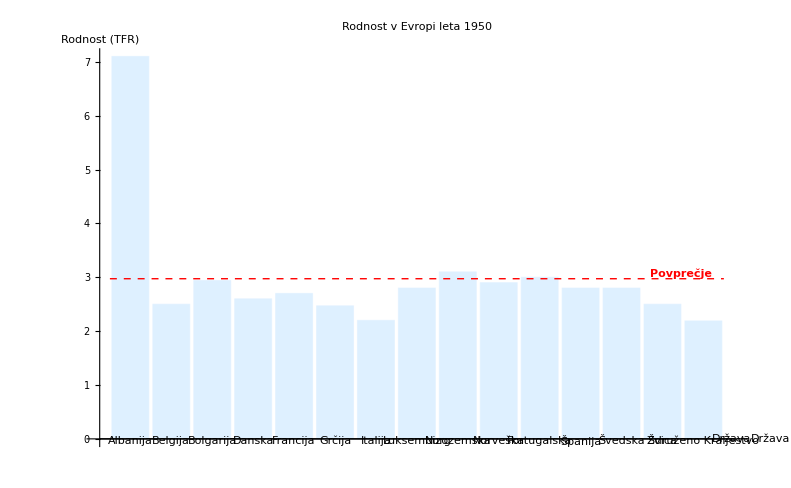

Povprečna rodnost v Evropi leta 1950: 2.97

```mathematica
povp50 = Mean[podatki50[[All,2]]];

BarChart[podatki50[[All, 2]], ChartLabels->Map[Style[#,Small]&,podatki50[[All,1]]], ChartStyle-> LightBlue, AxesLabel-> {"Država", "Rodnost (TFR)"}, PlotLabel-> "Rodnost v Evropi leta 1950", ImageSize-> Large, RotateLabel->True, Epilog-> {Red, Dashed, Line[{{0.5, povp50}, {15.5, povp50}}], Text[Style["Povprečje", Red, Bold], {15.2, povp50}, {1, -1}]}]

Print["Povprečna rodnost v Evropi leta 1950: ",NumberForm[povp50,{3,2}]];
```

### 1975

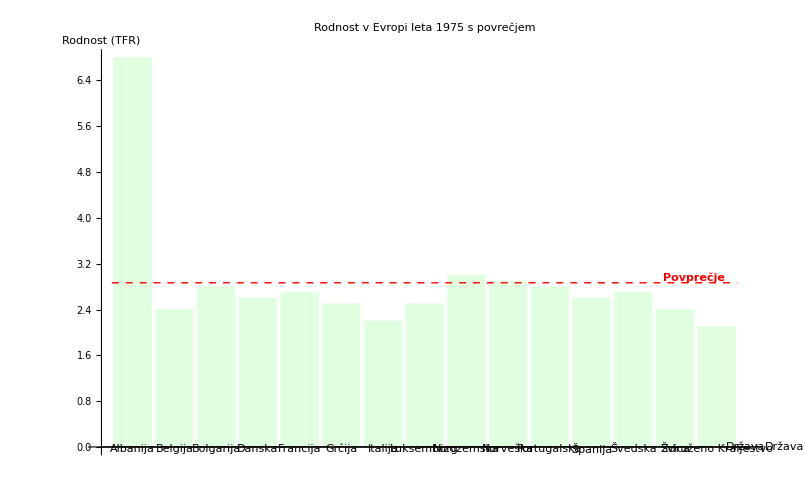

Povprečna rodnost v Evropi leta 1950: 2.87

```mathematica
povp75 = Mean[podatki75[[All,2]]];

BarChart[podatki75[[All, 2]], ChartLabels->Map[Style[#,Small]&, podatki75[[All,1]]],ChartStyle-> LightGreen, AxesLabel-> {"Država", "Rodnost (TFR)"}, PlotLabel-> "Rodnost v Evropi leta 1975 s povrečjem", ImageSize-> Large, RotateLabel->True, Epilog-> {Red, Dashed, Line[{{0.5, povp75}, {15.5, povp75}}], Text[Style["Povprečje", Red, Bold], {15.2, povp75}, {1, -1}]}]

Print["Povprečna rodnost v Evropi leta 1950: ",NumberForm[povp75,{3,2}]];
```

### 2000

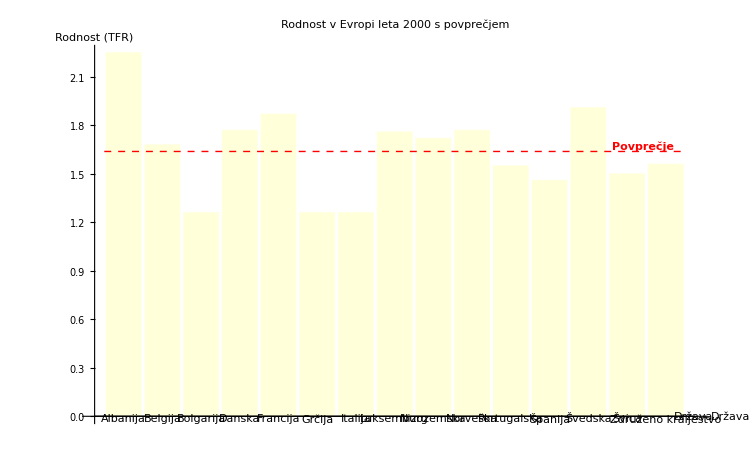

Povprečna rodnost v Evropi leta 2000: 1.64

```mathematica
povp00=Mean[podatki00[[All,2]]];

BarChart[podatki00[[All,2]],ChartLabels->Map[Style[#,Small]&,podatki00[[All,1]]],ChartStyle->LightYellow,AxesLabel->{"Država","Rodnost (TFR)"},PlotLabel->"Rodnost v Evropi leta 2000 s povprečjem",ImageSize->Large,RotateLabel->True,Epilog-> {Red, Dashed, Line[{{0.5, povp00}, {15.5, povp00}}], Text[Style["Povprečje", Red, Bold], {15.2, povp00}, {1, -1}]}]

Print["Povprečna rodnost v Evropi leta 2000: ",NumberForm[povp00,{3,2}]];
```

### 2023

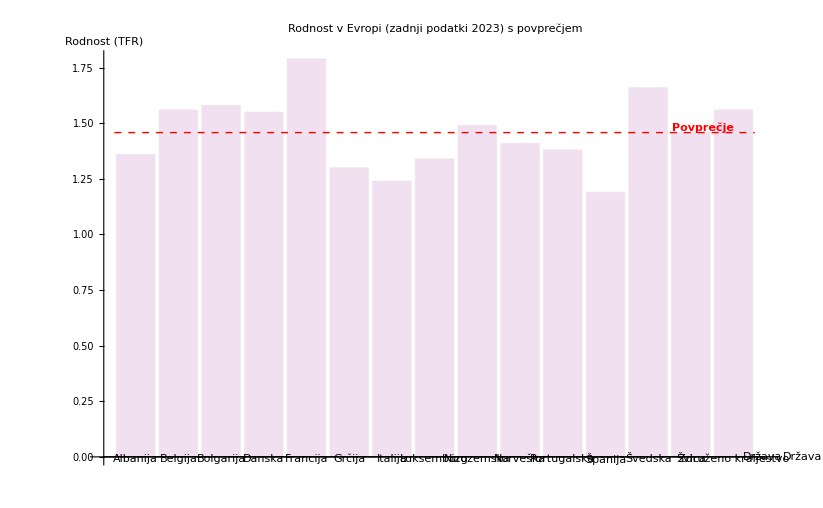

Povprečna rodnost v Evropi (2023): 1.46

```mathematica
povp23=Mean[podatki23[[All,2]]];

BarChart[podatki23[[All,2]],ChartLabels->Map[Style[#,Small]&,podatki23[[All,1]]],ChartStyle->LightPurple,AxesLabel->{"Država","Rodnost (TFR)"},PlotLabel->"Rodnost v Evropi (zadnji podatki 2023) s povprečjem",ImageSize->Large,RotateLabel->True,Epilog->{Red,Dashed,Line[{{0.5,povp23},{Length[podatki23]+0.5,povp23}}],Text[Style["Povprečje",Red,Bold],{Length[podatki23],povp23},{1,-1}]}]

Print["Povprečna rodnost v Evropi (2023): ",NumberForm[povp23,{3,2}]];
```

### Ugotovitev

Rodnost se nenehno znižuje in je še posebaj nizka v današnjem času.

## Animirani graf za Slovenijo

```mathematica
ListAnimate[Table[Module[{pt,povp},pt=Select[slovenija,#[[1]]<=yr&];
povp=Mean[pt[[All,2]]];
Graphics[{LightBlue,Rectangle[{#[[1]]-0.4,0},{#[[1]]+0.4,#[[2]]}]&/@pt,Red,Dashed,Line[{{1950-0.5,povp},{yr+0.5,povp}}],Text[Style["Povprečje: "<>ToString[NumberForm[povp,{3,2}]],Red,Bold],{yr,povp},{0,-1}]},Axes->True,PlotRange->{{1949,2025},{0,3.5}},ImageSize->Large,PlotLabel->"Rodnost v Sloveniji do leta "<>ToString[yr],Ticks->{Range[1950,2025,5],Automatic}]],{yr,1950,2023}],AnimationRate->1,DefaultDuration->25]
```

## Prikaz stanja najpogostejših dejavnikov, ki vplivajo na rodnost

```mathematica
dejavniki={{"Kategorija","Glavni dejavniki","Vpliv na rodnost"},{"Gospodarski","Gospodarska rast, brezposelnost, dohodek","Višji dohodek in nižja brezposelnost → višja rodnost"},{"Socialni / kulturni","Izobraževanje žensk, urbanizacija, spremembe družinske kulture","Kasnejše rojstvo otrok in manj otrok na družino"},{"Zdravstveni","Dostop do kontracepcije, zdravstvena oskrba","Manj neplaniranih rojstev, višja preživetost otrok"},{"Politični / institucionalni","Družinska politika, otroški dodatki, porodniški dopust","Podpora družinam povečuje rodnost"},{"Demografski","Starost mater, staranje prebivalstva","Višja starost pri prvem otroku → nižja rodnost"}};

Grid[dejavniki,Frame->All,Alignment->Left,Spacings->{2,1}]
```

Kategorija | Glavni dejavniki | Vpliv na rodnost
Gospodarski | Gospodarska rast, brezposelnost, dohodek | Višji dohodek in nižja brezposelnost → višja rodnost
Socialni / kulturni | Izobraževanje žensk, urbanizacija, spremembe družinske kulture | Kasnejše rojstvo otrok in manj otrok na družino
Zdravstveni | Dostop do kontracepcije, zdravstvena oskrba | Manj neplaniranih rojstev, višja preživetost otrok
Politični / institucionalni | Družinska politika, otroški dodatki, porodniški dopust | Podpora družinam povečuje rodnost
Demografski | Starost mater, staranje prebivalstva | Višja starost pri prvem otroku → nižja rodnost

## Aplikacija v oblaku

```mathematica
evropa=<|1975->1.94,1976->1.89,1977->1.86,1978->1.84,1979->1.84,1980->1.85,1981->1.82,1982->1.79,1983->1.76,1984->1.73,1985->1.67,1986->1.62,1987->1.59,1988->1.58,1989->1.57,1990->1.55,1991->1.54,1992->1.51,1993->1.47,1994->1.44,1995->1.43,1996->1.42,1997->1.42,1998->1.44,1999->1.46,2000->1.50,2001->1.48,2002->1.47,2003->1.48,2004->1.50,2005->1.52,2006->1.54,2007->1.56,2008->1.60,2009->1.59,2010->1.57,2011->1.57,2012->1.58,2013->1.55,2014->1.56,2015->1.58,2016->1.60,2017->1.59,2018->1.54,2019->1.53,2020->1.50,2021->1.53,2022->1.46,2023->1.38|>;

CloudDeploy[FormFunction["leto"->"Integer",With[{izbraniPodatek= evropa[#leto]},If[KeyExistsQ[evropa,#leto],StringTemplate["Leta `` je bila povprečna rodnost `` otroka na žensko."][#leto,izbraniPodatek],"Za izbrano leto ni podatkov. Prosim, vnesite leto med 1975 in 2023."]]&],"RodnostAplikacija"]
```

CloudObject[https://www.wolframcloud.com/obj/pt42710/RodnostAplikacija]